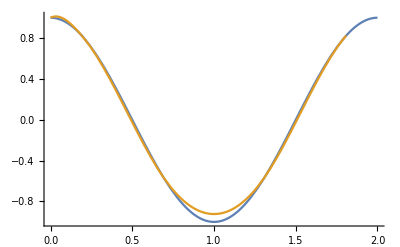

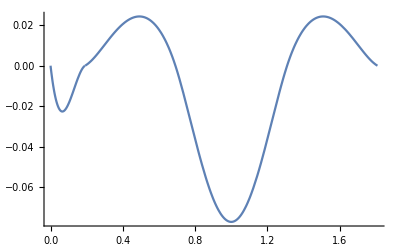

General::stop: Further output of Set::write will be suppressed during this calculation.

Set::write: Tag C in C[3] is Protected.

Set::write: Tag C in C[2] is Protected.

Set::write: Tag C in C[1] is Protected.

Set::write: Tag C in C[2] is Protected.

Set::write: Tag C in C[3] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

```mathematica
(* Йорданка *)
(* брой възли *)
n=5;

(* Дефиниране на функцията f,която ще бъде интерполирана от търсения естествен кубичен сплайн *)
f[t_]:=Cos[Pi*t];

(* Инициализация на възлите хk k=0,..n *)
Do[x[k]=2*(Sin[(k*Pi)/(2*n)])^2,{k,0,n}];

(* Пресмятаме разстоянието между всеки два съседни възела *)
Do[h[k]= x[k+1]-x[k],{k,0,n-1}];

(* Решаваме системата по метода на прогонката *)
(* Изчисляваме корфициентите *)
Do[coefA[k]= 1/h[k-1],{k,2,n-1}];
Do[coefB[k]= 2/h[k-1]+2/h[k],{k,1,n-1}];
Do[coefC[k]= 1/h[k],{k,1,n-2}];
Do[value[k] = 3*(f[x[k]]-f[x[k-1]])/(h[k-1])^2 + 3*(f[x[k+1]]-f[x[k]])/(h[k])^2,{k,1,n-1}];

(* Изчисляваме алфа и бета *)
alpha[1]=-coefC[1]/coefB[1];
beta[1]=value[1]/coefB[1];
Do[alpha[k]=-coefC[k]/(coefA[k]*alpha[k-1]+coefB[k]),{k,2,n-2}];
Do[beta[k]= (value[k]-coefA[k]*beta[k-1])/(coefA[k]*alpha[k-1]+coefB[k]),{k,2,n-1}];

(* Намираме s[0] и s[n] чрез втората производна на интерполиращия полином *)
s[0]=3*(f[x[1]]-f[x[0]])/2*h[1] - s[1]/2;
s[n]=3*(f[x[n]]-f[x[n-1]])/2*h[n] - s[n-1]/2;
s[n-1]=beta[n-1];

Do[s[k]=alpha[k]*s[k+1]+beta[k],{k,n-2,1,-1}]; (* стъпка: -1 *)
Do[a[k]=s[k+1]/h[k]^2 + s[k]/h[k]^2 + 2*(f[x[k]]-f[x[k+1]])/h[k]^3,{k,0,n-1}];
Do[b[k]=(f[x[k+1]]-f[x[k]])/h[k]^2-s[k]/h[k],{k,0,n-1}];

(* Общ вид на полиномите,интерполиращи f(t) във всеки подинтервал на [0,2], определен от два последователни интерполационни възела *)
Do[spolinom[k,z_]=a[k]*(z-x[k])^2*(z-x[k+1])+b[k]*(z-x[k])^2+s[k]*(z-x[k])+f[x[k]],{k,0,n-1}];

(* Построяване на кубичния сплайн за f(t), като вече имаме интерполиращите полиноми за всеки един интервал *)
rec[i_,t_]:=If[i≤n+1,If[t≥x[i] && t<x[i+1],spolinom[i,t],rec[i+1,t]]];
spline[t_]:=rec[0,t];

(* Визуализация на графиките на функцията и сплайн функцията *)
Plot[{f[t],spline[t]},{t,0,2},PlotRange-> All]

(* Визуализация на графиката на разликата от функцията и сплайн функцията *)
Plot[f[t]-spline[t],{t,0,2},PlotRange->All]
```